```mathematica
n=5;
On[Assert];
(*Convert an index in our space to a one-hot set of occupied sites*)
iToS[i_]:=Block[{},Assert[1≤i≤2^n];PadLeft[IntegerDigits[i-1,2],n]];
(*Convert a bitset back to an index*)
sToI[s_]:=Block[{},Assert[AllTrue[s,#==0||#==1&]];1+FromDigits[s,2]];

(*Annihilation operator on a given site*)
a[site_]:=Block[{entries={}},
Do[
Block[{set=iToS[i]},
If[set[[site]]==1,
set[[site]]=0;
AppendTo[entries,{sToI[set],i}->
(-1)^(Total[set[[1;;site-1]]])]]],
{i,2^n}];
SparseArray[entries,{2^n,2^n}]
]

(*Creation operator on a given site*)
aD[site_]:=Block[{entries={}},
Do[
Block[{set=iToS[i]},
If[set[[site]]==0,
set[[site]]=1;
AppendTo[entries,{sToI[set],i}->
(-1)^(Total[set[[1;;site-1]]])]]],
{i,2^n}];
SparseArray[entries,{2^n,2^n}]
]
```

```mathematica
{a[1].a[2]==-a[2].a[1],
a[2].a[2]==SparseArray[{},{2^n,2^n}],
a[3].a[5]==-a[5].a[3],
a[3].a[4]!=-a[5].a[3],

aD[1].aD[2]==-aD[2].aD[1],
aD[2].aD[2]==SparseArray[{},{2^n,2^n}],
aD[3].aD[5]==-aD[5].aD[3],
aD[3].aD[4]!=-aD[5].aD[3],
aD[1].a[1]+a[1].aD[1]==IdentityMatrix[2^n],
Total[Sort[Eigenvalues[aD[3].a[3]]]]==2^(n-1),
Total[Sort[Eigenvalues[aD[1].a[1]]]]==2^(n-1)}
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
tFromRule[rule_]:=rule[[2]]aD[rule[[1,1]]].a[rule[[1,2]]];
uFromRule[rule_]:=rule[[2]]aD[rule[[1,1]]].aD[rule[[1,2]]].a[rule[[1,3]]].a[rule[[1,4]]]
```

```mathematica
Htu[t_,u_]:=Total[tFromRule/@(Most[ArrayRules[t]])]+Total[uFromRule/@(Most[ArrayRules[u]])]
```

```mathematica
test1[a_]:=Block[{H,T,U},
n=1;
H=N[Htu[{{a}},{}]];
Min[Eigenvalues[H]]
];
test2[a11_,a22_,a12_]:=Block[{H,T,U},
n=2;
T={{a11,a12},{a12,a22}};
H=N[Htu[T,{}]];
Min[Eigenvalues[H]]
];
testU[a11_,a22_,a12_,u_]:=Block[{H,T,U},
n=2;
T={{a11,a12},{a12,a22}};
U=SparseArray[{1,2,1,2}->u];
H=N[Htu[T,U]];
Min[Eigenvalues[H]]
];
testU3[w_,x_,y_,z_,u1212_,u1313_,u2323_,u1323_]:=Block[{T,U},
n=3;
T={{x,w,0},{w,y,0},{0,0,z}};
U=SparseArray[{
{1,2,1,2}->u1212,
{1,3,1,3}->u1313,
{2,3,2,3}->u2323,
{1,3,2,3}->u1323/2,
{2,3,1,3}->u1323/2
},{n,n,n,n}];
H=N[Htu[T,U]];
Min[Eigenvalues[H]]
];
testU3A[w1_,w2_,w3_,x_,y_,z_,u1212_,u1313_,u2323_,u1323_,u2123_]:=Block[{T,U},
n=3;
T={{x,w1,w2},{w1,y,w3},{w2,w3,z}};
U=SparseArray[{
{1,2,1,2}->u1212,
{1,3,1,3}->u1313,
{2,3,2,3}->u2323,
{1,3,2,3}->u1323/2,
{2,3,1,3}->u1323/2,
{2,1,2,3}->u2123/2,
{2,3,2,1}->u2123/2
},{n,n,n,n}];
H=N[Htu[T,U]];
Min[Eigenvalues[H]]
];
testU4A[w1_,w2_,w3_,w4_,w5_,w6_,v_,x_,y_,z_,u1212_,u1313_,u2323_,u2424_,u3434_,u1323_,u2123_,u1234_,u2124_,u1324_,u2423_]:=Block[{T,U},
n=4;
T={{v,w1,w2,w3},{w1,x,w4,w5},{w2,w4,y,w6},{w3,w5,w6,z}};
U=SparseArray[{
{1,2,1,2}->u1212,
{1,3,1,3}->u1313,
{2,3,2,3}->u2323,
{2,4,2,4}->u2424,
{3,4,3,4}->u3434,

{1,3,2,3}->0*u1323/2,
{2,3,1,3}->0*u1323/2,

{2,1,2,3}->0*u2123/2,
{2,3,2,1}->0*u2123/2,

{1,2,3,4}->0*u1234/2,
{3,4,1,2}->0*u1234/2,

{2,1,2,4}->0*u2124/2,
{2,4,2,1}->0*u2124/2,

{1,3,2,4}->0*u1324/2,
{2,4,1,3}->0*u1324/2,

{2,4,2,3}->0*u2423/2,
{2,3,2,4}->0*u2423/2
},{n,n,n,n}];
H=N[Htu[T,U]];
Min[Eigenvalues[H]]
];
```

```mathematica
{test1[-10]==-10.,
test1[+10]==0.0,
test2[-3,+4,0]==-3.0,
test2[+3,+4,0]==0.0,
test2[-3,-4,0]==-7.0,
test2[-3,-4,1]==-7.0,
Abs[test2[-3,-4,100000]-(-100003.5)]<1*^-5,
testU[0,0,0,1.0]==-1.0,
testU[-3,-4,0,1.0]==-8.0}

testU[-3,-4,0,-1.0]
testU[-3,0,-4,+1.0]
```

{True,True,True,True,True,True,True,True,True}

-6.

-5.772

```mathematica
(*1D Hubbard model. Compare with hubbard.jl*)
```

```mathematica
Hubbard1D[nSites_,hoppingT_,onsiteU_,periodic_]:=Block[{T,U,H,i2,e0},
n=2*nSites;
T=Array[0&,{n,n}];
U=SparseArray[{},{n,n,n,n}];
e0=0;
Do[
If[i+1<n||periodic,
i2=If[i+1<n,i+2,i+2-n];
T[[i,i2]]-=hoppingT;
T[[i2,i]]-=hoppingT;
]
,{i,n}];
Do[
i2=i+1;
U[[i,i2,i2,i]]+=onsiteU;
T[[i,i]]-=onsiteU/2;
T[[i2,i2]]-=onsiteU/2;
e0+=onsiteU/4;
,{i,1,n,2}];
H=N[Htu[T,U]];
H+e0 SparseArray[{{i_,i_}->offset},{2^n,2^n}]
];
```

```mathematica
HubbardE[nSites_,u_]:=Block[{},
offset=1;
H=Hubbard1D[nSites,1,u,True];
H-=SparseArray[{i_,i_}->offset,{2^n,2^n}];
Eigenvalues[H,1][[1]]+offset
]
```

```mathematica
HubbardE[3,0.5]
```

-3.96733

```mathematica
Edata3=Table[{u,HubbardE[3,u]},{u,-2.7,2.7,0.3}]
```

{{-2.7,-4.525},{-2.4,-4.43549},{-2.1,-4.35387},{-1.8,-4.28019},{-1.5,-4.21445},{-1.2,-4.15657},{-0.9,-4.10641},{-0.6,-4.06376},{-0.3,-4.02839},{-4.44089×10^-16,-4.},{0.3,-3.97828},{0.6,-3.96288},{0.9,-3.95344},{1.2,-3.94962},{1.5,-3.95103},{1.8,-3.95735},{2.1,-3.96821},{2.4,-3.98329},{2.7,-4.0023}}

```mathematica
Edata4=Table[{u,HubbardE[4,u]},{u,-2.7,2.7,0.3}]
```

{{-2.7,-5.23596},{-2.4,-5.05548},{-2.1,-4.88365},{-1.8,-4.72123},{-1.5,-4.56907},{-1.2,-4.42809},{-0.9,-4.29938},{-0.6,-4.18416},{-0.3,-4.08383},{-4.44089×10^-16,-4.},{0.3,-4.08383},{0.6,-4.18416},{0.9,-4.29938},{1.2,-4.42809},{1.5,-4.56907},{1.8,-4.72123},{2.1,-4.88365},{2.4,-5.05548},{2.7,-5.23596}}

```mathematica
Edata5=Table[{u,HubbardE[5,u]},{u,-2.7,2.7,0.3}]
```

{{-2.7,-7.19223},{-2.4,-7.05133},{-2.1,-6.92606},{-1.8,-6.81639},{-1.5,-6.72217},{-1.2,-6.64314},{-0.9,-6.57899},{-0.6,-6.52936},{-0.3,-6.49388},{-4.44089×10^-16,-6.47214},{0.3,-6.46374},{0.6,-6.4683},{0.9,-6.4854},{1.2,-6.51461},{1.5,-6.55552},{1.8,-6.60765},{2.1,-6.67055},{2.4,-6.74372},{2.7,-6.82665}}

```mathematica
Edata6={{-8.,-14.0481},{-6.8,-12.5725},{-5.6,-11.2099},{-4.4,-10.0165},{-3.2,-9.06406},{-2.7,-8.75336},{-2.4,-8.59289},{-2.1,-8.45205},{-2.,-8.40946},{-1.8,-8.33076},{-1.5,-8.22882},{-1.2,-8.14595},{-0.9,-8.08187},{-0.8,-8.06464},{-0.6,-8.03631},{-0.3,-8.00907},{0,-8.},{0.3,-8.00907},{0.4,-8.01612},{0.6,-8.03631},{0.9,-8.08187},{1.2,-8.14595},{1.5,-8.22882},{1.6,-8.26066},{1.8,-8.33076},{2.1,-8.45205},{2.4,-8.59289},{2.7,-8.75336},{2.8,-8.8112},{4.,-9.66871},{5.2,-10.7899},{6.4,-12.1034},{7.6,-13.5463}};
```

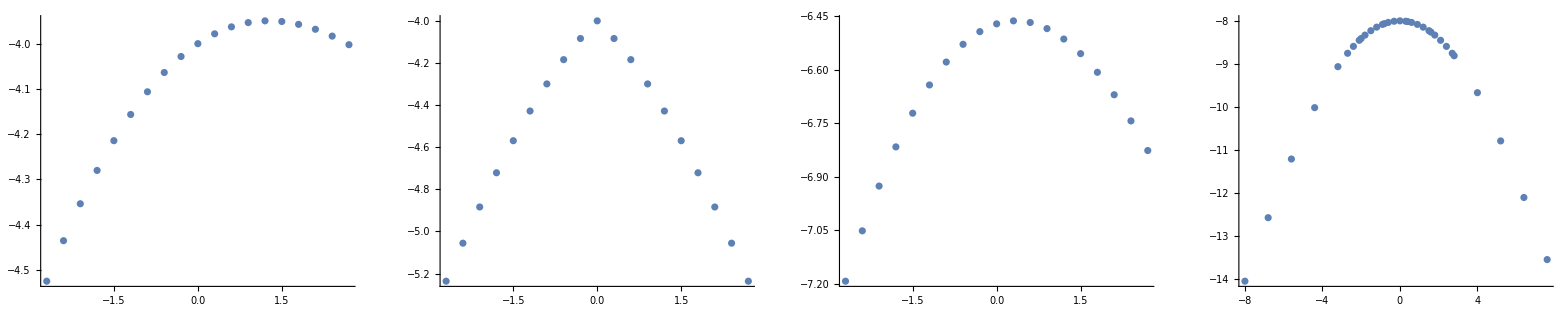

```mathematica
GraphicsGrid@List@(ListPlot/@{Edata3,Edata4,Edata5,Edata6})
```

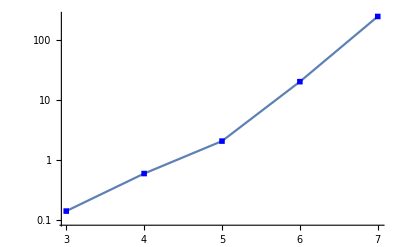

```mathematica
timesPerPoint={{3,0.1406},{4,0.5937},{5,2.0625},{6,20.187},{7,246.578}};
ListLogPlot[timesPerPoint,Joined->True,PlotMarkers->Style["■", Large, Blue]]
```

```mathematica
HubbardE[3,0.3]//Timing
```

{0.140625,-3.97828}

```mathematica
HubbardE[4,0.3]//Timing
```

{0.59375,-4.08383}

```mathematica
HubbardE[5,0.3]//Timing
```

{2.0625,-6.46374}

```mathematica
HubbardE[6,0.3]//Timing
```

{20.1875,-8.00907}

```mathematica
HubbardE[7,0.3]//Timing
```

{246.578,-8.98705}

```mathematica
{xs,gHF3,gHF4,gHF5,gHF6,gHF7,gHF8}=Transpose[Import["./UCSB_G1/GMPS/hubbard1D_dumbTest.csv"]];
```

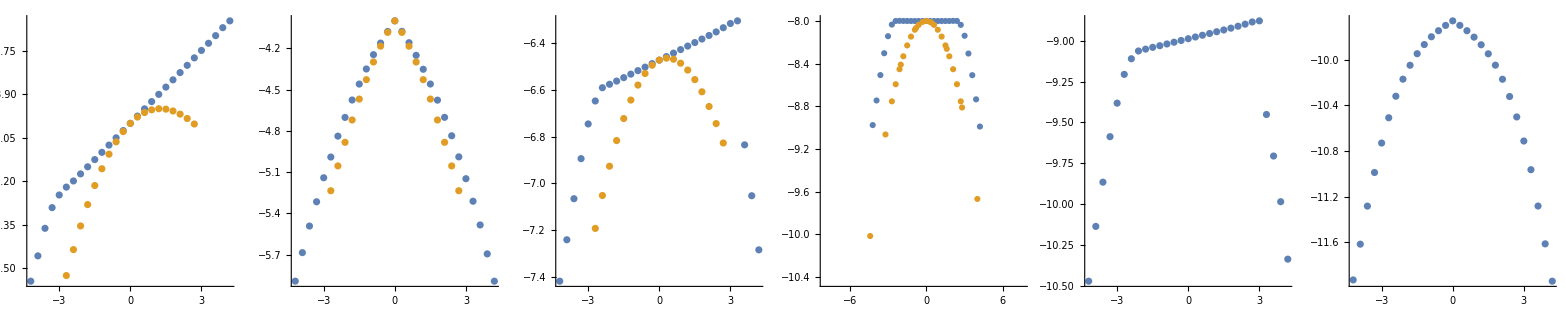

```mathematica
GraphicsGrid@(List@((
ListPlot[{Transpose[{xs,#2}],#1}]
&@@@{{Edata3,gHF3,3},{Edata4,gHF4,4},{Edata5,gHF5,5},{Edata6,gHF6,6}})~Join~{ListPlot[Transpose[{xs,gHF7}]],ListPlot[Transpose[{xs,gHF8}]]}))
```

```mathematica
Transpose[{xs,gHF4}][[9]]
```

{-1.8,-4.57601}

```mathematica
Edata4[[4]]
```

{-1.8,-4.72123}

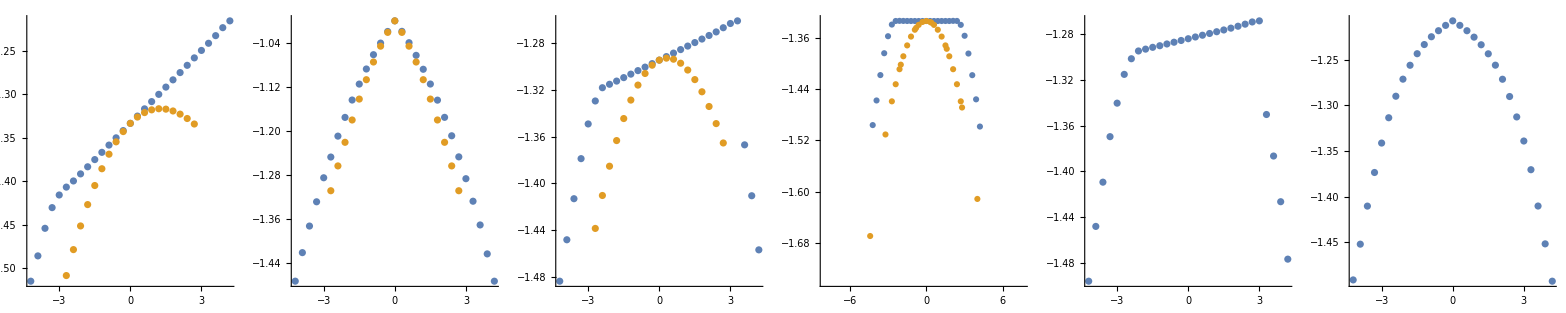

```mathematica
(*Normalized energy per site -- better for comparing different system sizes*)
GraphicsGrid@(List@((
ListPlot[{Transpose[{xs,#2/#3}],Transpose[{#1[[;;,1]],#1[[;;,2]]/#3}]}]
&@@@{{Edata3,gHF3,3},{Edata4,gHF4,4},{Edata5,gHF5,5},{Edata6,gHF6,6}})~Join~{ListPlot[Transpose[{xs,gHF7/7}]],ListPlot[Transpose[{xs,gHF8/8}]]}))
```

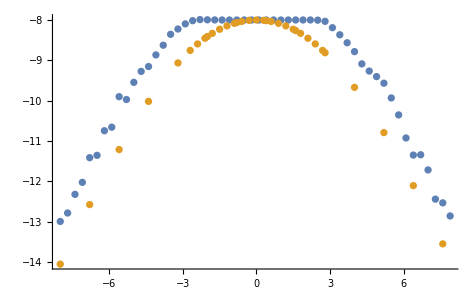

```mathematica
ListPlot[{Transpose@{xs,gHF},%200~Join~Edata5N}]
```

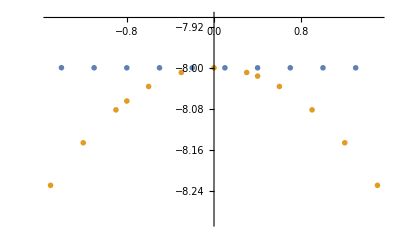

```mathematica
ListPlot[{Transpose@{xs,gHF},%200~Join~Edata5N},PlotRange->{{-1.5,1.5},{-8.3,-7.9}},MeshStyle->Directive[PointSize[10]],PlotMarkers->{Blue,Orange,Orange}]
```